```mathematica
f[x_] := (x^2 - 1)*Tan[x]
```

```mathematica
(* Nullstellen *)
Solve[Reduce[{f[x]==0,-Pi/2<=x<= Pi/2}], x]
```

{{x→-1},{x→0},{x→1}}

```mathematica
(* Extremwerte *)
Solve[f'[x]==0, x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(-1+x^2) Sec[x]^2+2 x Tan[x]==0,x]

```mathematica
(* Solve kann die Gleichung nicht lösen -> Numerisch die Extrempuntke finden *)
(* 1 und -1 kommen von den geplotten Funktionen weiter unten *)
FindRoot[f'[x]==0,{x,{1,-1}}]
```

{x→{0.631264,-0.631264}}

```mathematica
(* Singularitäten *)
FunctionDomain[f[x], x]
Reduce[! FunctionDomain[f[x], x]]
Reduce[{! FunctionDomain[f[x], x], -Pi/2<=x<= Pi/2}]
Solve[x/Pi==-1/2, x]
```

1/2+x/π∉Integers

1/2+x/π∈Integers&&x∈Reals

1/2+x/π∈Integers&&-π/2≤x≤π/2

{{x→-π/2}}

```mathematica
N[%268]
```

0.5+0.31831 x∉Integers

```mathematica
(* Wendepunkte *)
wp=Solve[Reduce[{f''[x]==0,-Pi/2<=x<= Pi/2}],x] (* Wendepunkte berechnen (eigentlich nur deren x-Werte)*)
ws={x}/.wp[[1]] (* x-Werte extrahieren *)
DeleteCases[ws,x_/;f'''[x]==0] (* Stellen löschen, wenn die 3. Ableitung 0 ist*)
toPoint[x_]:={x,f[x]} (* Hilfsfunktion um aus x-Stellen Punkte zu berechnen *)
toPoint[ws] (* Punkte berechnen *)
```

{{x→0}}

{0}

{0}

{{0},{0}}

```mathematica
(* Plotten von f, f' und f'' *)
```

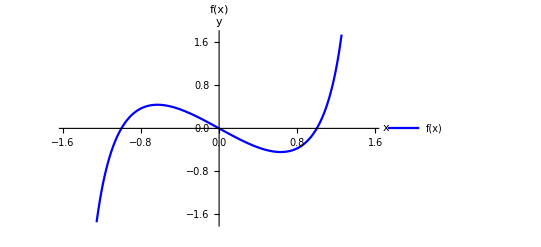

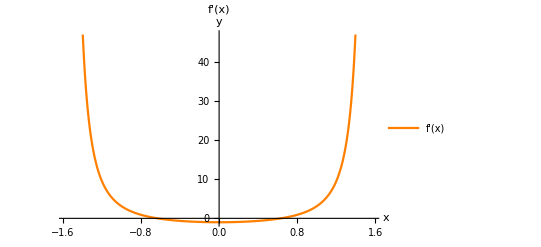

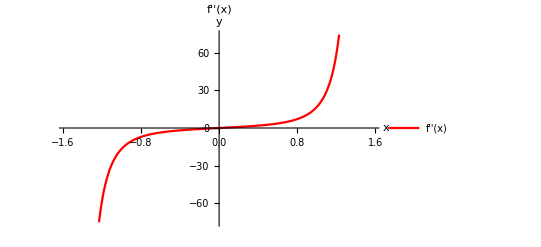

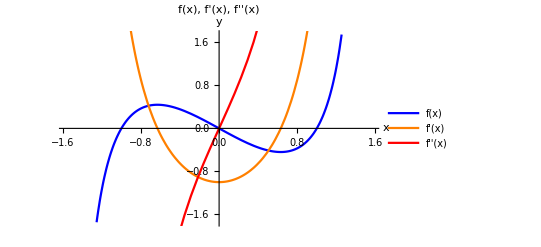

```mathematica
myPlot[a_,b_] := Plot[a, {x, -Pi/2, Pi/2}, b, AxesLabel->{"x","y"}] (* Hilfsfunktion um redudanten Code zu vermeiden *)
d0 = myPlot[f[x],{ PlotLegends->{"f(x)"},PlotStyle->Blue,PlotLabel->"f(x)"}] (* Funktion f plotten und in d0 ablegen *)
d1 = myPlot[f'[x], { PlotLegends->{"f'(x)"},PlotStyle->Orange,PlotLabel->"f'(x)"}] (* Ableitung f' plotten und in d1 ablegen *)
d2 = myPlot[f''[x], { PlotLegends->{"f''(x)"},PlotStyle->Red,PlotLabel->"f''(x)"}] (* Ableitung f'' plotten und in d2 ablegen *)
Show[d0,d1,d2,PlotLabel->"f(x), f'(x), f''(x)"] (* d0, d1 und 2 gemeinsam plotten *)
```